```mathematica
I=Integrate[Exp[-2(x-i)^2/b^2]*(4/b^2 Exp[-2*(x-j)^2/b^2]+16/b^4(x-j)^2 Exp[-2(x-j)^2/b^2]),{x,-∞,∞}]
```

Set::wrsym: Symbol ⅈ is Protected.

```mathematica
i1=(ⅇ^(-(i-j)^2/b^2) (3 b^2+2 (i-j)^2) √π)/(√(1/b^2) b^4)
```

(ⅇ^(-(i-j)^2/b^2) (3 b^2+2 (i-j)^2) √π)/(√(1/b^2) b^4)

```mathematica
i1//FullSimplify
```

(ⅇ^(-(i-j)^2/b^2) (3 b^2+2 (i-j)^2) √π)/(√(1/b^2) b^4)

```mathematica
Integrate[Exp[-2(x-i)^2/b^2]*(-D*Exp[-2*(x-i)^2/c^2]-D*Exp[-2(x-j)^2/c^2])*Exp[-2*(x-j)^2/b^2],{x,-∞,∞}]
```

ConditionalExpression[-(D ⅇ^(-(2 (b^2+c^2) (i-j)^2)/(b^4+2 b^2 c^2)) √(2 π))/(√(2/b^2+1/c^2)),Re[-4/b^2-2/c^2]≤0]

```mathematica
i2=-(D ⅇ^(-(2 (b^2+c^2) (i-j)^2)/(b^4+2 b^2 c^2)) √(2 π))/(√(2/b^2+1/c^2))//FullSimplify
```

-(D ⅇ^(-(2 (b^2+c^2) (i-j)^2)/(b^4+2 b^2 c^2)) √(2 π))/(√(2/b^2+1/c^2))

```mathematica
F = Series[-D*Exp[-2*(x-b)^2]-D*Exp[-2(x+b)^2],{x,0,4}]//FullSimplify
```

-2 (D ⅇ^(-2 b^2))+4 (1-4 b^2) D ⅇ^(-2 b^2) x^2-4/3 ((3-24 b^2+16 b^4) D ⅇ^(-2 b^2)) x^4+O[x]^5

```mathematica
-24 *(.2)^2+16 (.2)^4
```

-0.9344

```mathematica
Series[-D*Exp[-2*(x)^2],{x,0,4}]//FullSimplify
```

-D+2 D x^2-2 D x^4+O[x]^5

```mathematica
4/3 (3-24 (.2)^2+16 (.2)^4)
```

2.75413

```mathematica
F2 = Series[-D*Exp[-2*(x-b)^2]-D*Exp[-2(x+b)^2],{x,0,8}]//FullSimplify
```

-2 (D ⅇ^(-2 b^2))+4 (1-4 b^2) D ⅇ^(-2 b^2) x^2-4/3 ((3-24 b^2+16 b^4) D ⅇ^(-2 b^2)) x^4-8/45 ((-15+180 b^2-240 b^4+64 b^6) D ⅇ^(-2 b^2)) x^6-4/315 ((105+16 b^2 (-105+2 b^2 (105+8 b^2 (-7+b^2)))) D ⅇ^(-2 b^2)) x^8+O[x]^9

```mathematica
V[x_,D_,b_]:= -D*Exp[-2*(x-b)^2]-D*Exp[-2(x+b)^2]
```

```mathematica
Vapprox[x_,D_,b_]:=-2 (D ⅇ^(-2 b^2))+4 (-4 b^2+1) D ⅇ^(-2 b^2) x^2-(4 ((16 b^4-24 b^2 +3 ) D ⅇ^(-2 b^2)) x^4)/3
```

```mathematica
Manipulate[Vapprox[x,1,b]//N,{b,0,2}]
```

```mathematica
Vapprox2[x_,D_,b_]:=-2 (D ⅇ^(-2 b^2))+4 (1-4 b^2) D ⅇ^(-2 b^2) x^2-4/3 ((3-24 b^2+16 b^4) D ⅇ^(-2 b^2)) x^4-8/45 ((-15+180 b^2-240 b^4+64 b^6) D ⅇ^(-2 b^2)) x^6-4/315 ((105+16 b^2 (-105+2 b^2 (105+8 b^2 (-7+b^2)))) D ⅇ^(-2 b^2)) x^8
```

```mathematica
Manipulate[Plot[{V[x,D,b],Vapprox[x,D,b],Vapprox2[x,D,b]},{x,-2,2},PlotRange->{{-20,20},{0,-20}}],{b,0,50},{D,0.1,50}]
```

```mathematica
BinMonNCom[n_] := Sum[n!*(-1)^((n-k)/2)/(2^((n-k)/2)*((n-k)/2)!*k!)KroneckerDelta[Mod[(n-k),2],0]*(a+b)^k,{k,0,n}]
```

```mathematica
BinMonNCom[4]//Expand
```

3-6 a^2+a^4-12 a b+4 a^3 b-6 b^2+6 a^2 b^2+4 a b^3+b^4

```mathematica
3!
```

6

```mathematica
BinMonNCom[6]//Expand
```

-15+45 a^2-15 a^4+a^6+90 a b-60 a^3 b+6 a^5 b+45 b^2-90 a^2 b^2+15 a^4 b^2-60 a b^3+20 a^3 b^3-15 b^4+15 a^2 b^4+6 a b^5+b^6

```mathematica
BinMonNCom[8]//Expand
```

105-420 a^2+210 a^4-28 a^6+a^8-840 a b+840 a^3 b-168 a^5 b+8 a^7 b-420 b^2+1260 a^2 b^2-420 a^4 b^2+28 a^6 b^2+840 a b^3-560 a^3 b^3+56 a^5 b^3+210 b^4-420 a^2 b^4+70 a^4 b^4-168 a b^5+56 a^3 b^5-28 b^6+28 a^2 b^6+8 a b^7+b^8

```mathematica
-4/3 ((3-24 b^2+16 b^4) D ⅇ^(-2 b^2))
```

```mathematica
Ψ2p[n_,x_,V_,c,b_] := Φ[n,x]/.{ω->Sqrt[2*4 (-4 b^2+1) V ⅇ^(-2 b^2) ],h->1,m->1}
```

```mathematica
P0[x_,V_,b_] := Ψ2p[0,x,V,1,b]-(4 ((16 b^4-24 b^2 +3 ) V*ⅇ^(-2 b^2)) *15*Sqrt[2])/(6*Sqrt[2*4 (1-4 b^2) V ⅇ^(-2 b^2) ])*Ψ2p[2,x,V,1,b]-(4 ((16 b^4-24 b^2 +3 ) V ⅇ^(-2 b^2)) *Sqrt[4!])/(12*Sqrt[2*4 (-4 b^2+1) V ⅇ^(-2 b^2) ])*Ψ2p[4,x,V,1,b]
```

```mathematica
P0[0,1,.1]
```

```mathematica
Manipulate[(4 ((16 b^4-24 b^2 +3 ) 1*ⅇ^(-2 b^2)) *15*Sqrt[2])/(6*Sqrt[2*4 (1-4 b^2) 1 ⅇ^(-2 b^2) ]),{b,0,2}]
```

```mathematica
Manipulate[Plot[P0[x,1,b]^2,{x,-.2,.2}],{b,0,2}]
```

```mathematica
P1[x_,V_,b_] := Ψ2p[1,x,V,1,b]-(4 ((16 b^4-24 b^2 +3 ) V*ⅇ^(-2 b^2)) *21*Sqrt[2])/(6*Sqrt[2*4 (-4 b^2+1) V ⅇ^(-2 b^2) ])*Ψ2p[3,x,V,1,b]-(4 ((16 b^4-24 b^2 +3 ) V ⅇ^(-2 b^2)) *Sqrt[5!])/(12*Sqrt[2*4 (-4 b^2+1) V ⅇ^(-2 b^2) ])*Ψ2p[5,x,V,1,b]
```

```mathematica
Manipulate[Plot[Abs[P1[x,1,b]+P0[x,1,b]]^2,{x,-2,2}],{b,0,2}]
```

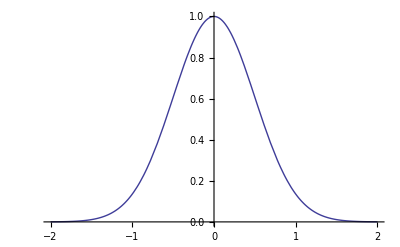

```mathematica
Plot[Exp[-2*x^2],{x,-2,2}]
```